# Active SSH

### Preamble

```mathematica
(*ClearAll["Global`*"];*)
SetDirectory[NotebookDirectory[]]; (* or else the default directory is Directory[]*)
myEliminate[sys_,var_]:=Module[{sol},
sol=Solve[sys[[1]],var][[1]];
sys[[2;;-1]]/.sol
];
```

### Parameters

```mathematica
Mms=6.7*^-4; (*0.5*)
Rms=0.26*0.2;(*0.09*)
Cmc=2.13*^-4;(*1/0.42*)
fres = 1/(2*Pi*Sqrt[Mms*Cmc])

sd=12*^-4;(* m^2 diaphragm surface *)
S=0.05*0.05; (*  m^2 duct cross section*)
rho0=1.184;(*[kg/m^3]*)
c0=346;(*%[m/s]*)
a=0.2806;(*[m]*)
kk =1*(-sd); (*Coupling negative*)
f0 =c0/a (*cutoff frequency*)

zs[k_] := (ⅈ  k c0)*Mms + Rms + 1/( (ⅈ  k c0)*Cmc);
zr:= rho0 c0 sd/S;
```

421.301

1233.07

### Speaker mechanical impedance

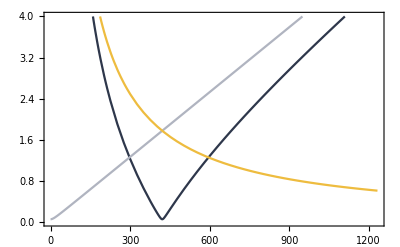

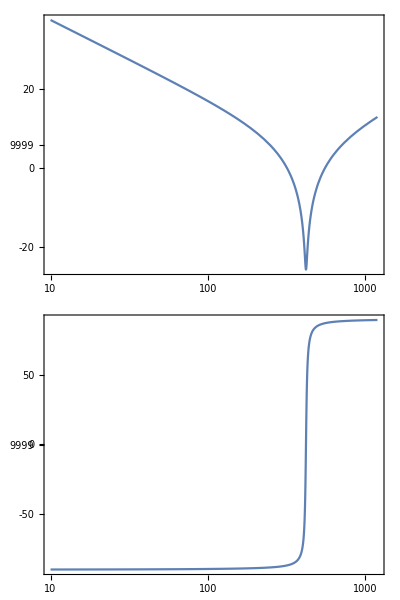

```mathematica
Zms[freq_]:= (I*2*Pi*freq)*Mms + Rms + 1/((I*2*Pi*freq)*Cmc);
ZmsAbv[freq_]:= (I*2*Pi*freq)*Mms + Rms ;
ZmsBlw[freq_]:=  Rms + 1/((I*2*Pi*freq)*Cmc);

Plot[{Abs[Zms[freq] ] ,Abs[ZmsAbv[freq]] ,Abs[ZmsBlw[freq] ]},{freq,0.1,f0},PlotRange->{{0,f0},{0,4}},PlotStyle->{ColorData["GrayYellowTones",0],ColorData["GrayYellowTones",0.5],ColorData["GrayYellowTones",1]},Frame->True]
BodePlot[Zms[f],{f,10,1200}]
```

### Transfer Matrix

#### Wave Guide section

```mathematica
T1[k_] := ({{Exp[-I k a/4], 0}, {0, Exp[+I k a/4]}});
```

#### Active section

```mathematica
(*coupled_ER_DIRECT__TM-004.nb*)
T2[k_]:= ({{((-1+ⅇ^(ⅈ a k)) (kk-sd) (kk+sd) zr^2+4 zs[k] (ⅇ^((ⅈ a k)/2) kk zr-sd zr+zs[k]))/(2 zs[k] ((-1+ⅇ^(ⅈ a k)) kk zr+2 ⅇ^((ⅈ a k)/2) zs[k])), (zr ((kk-sd) (kk+sd) zr Sin[(a k)/2]-2 ⅈ (kk-sd Cos[(a k)/2]) zs[k]))/(2 (kk zr Sin[(a k)/2]-ⅈ zs[k]) zs[k])}, {(zr ((-kk^2+sd^2) zr Sin[(a k)/2]+2 ⅈ (kk-sd Cos[(a k)/2]) zs[k]))/(2 (kk zr Sin[(a k)/2]-ⅈ zs[k]) zs[k]), -((-1+ⅇ^(ⅈ a k)) (kk-sd) (kk+sd) zr^2+4 ⅇ^((ⅈ a k)/2) kk zr zs[k]-4 ⅇ^(ⅈ a k) zs[k] (sd zr+zs[k]))/(2 zs[k] ((-1+ⅇ^(ⅈ a k)) kk zr+2 ⅇ^((ⅈ a k)/2) zs[k]))}});
```

#### Total transfer matrix

```mathematica
Ttot[k_]= T1[k].T2[k].T1[k];
```

```mathematica
M11[k_]:= Part[Ttot[k],1,1];
M12[k_]:= Part[Ttot[k],1,2];
M21[k_]:= Part[Ttot[k],2,1];
M22[k_]:= Part[Ttot[k],2,2];
M[k_]:= {{M11[k],M12[k]},{M21[k],M22[k]}} ;

MatrixForm[M[k]];
```

### Scattering Matrix

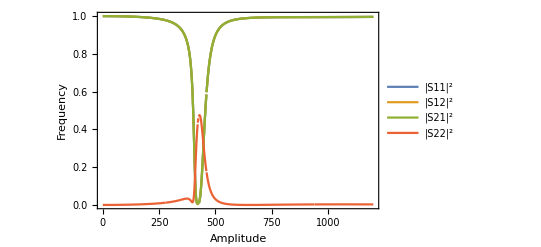

```mathematica
(*SS[k_]:= {{-M21[k]/M22[k],1/M22[k]},{M11[k]-M12[k]*M21[k]/M22[k],M12[k]/M22[k]}}*)
S11[k_]:= -M21[k]/M22[k];
S12[k_]:=1/M22[k];
S21[k_]:=M11[k]-M12[k]*M21[k]/M22[k];
S22[k_]:=M12[k]/M22[k];
SS[k_]:={{S11[k],S12[k]},{S21[k],S22[k]}} ;

(*MatrixForm[SS[k]]//FullSimplify*)

Plot[{
Abs[S12[2*Pi*freq/c0]]^2,
Abs[S12[2*Pi*freq/c0]]^2,
Abs[S21[2*Pi*freq/c0]]^2,
Abs[S22[2*Pi*freq/c0]]^2
},{freq,0.1,1200},PlotRange->{{0,1200},{0,1}},Frame->True, PlotLegends->{"|S11|^2","|S12|^2","|S21|^2","|S22|^2"},AxesLabel->{"Amplitude","Frequency"}]
```

### Effective density and bulk modulus

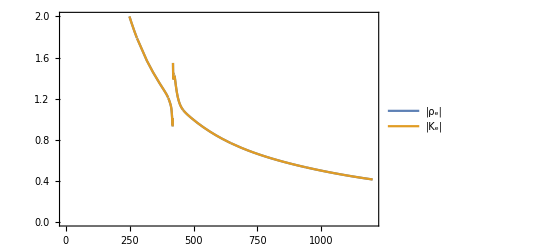

```mathematica
Ze[k_]:= Sqrt[((1+S11[k])^2-S21[k]^2)/((1+S11[k])^2-S21[k]^2)];(* Effective impedance plus-minus*)
n[k_]:= ArcCos[(1-S11[k]^2-S21[k]^2)/(2 S21[k])+2π]/(k a);(*Effective refractive index plus-minus*)

Plot[{
Abs[n[2*Pi*freq/c0]*Ze[2*Pi*freq/c0]],
Abs[n[2*Pi*freq/c0]/Ze[2*Pi*freq/c0]]
},{freq,0.1,1200},PlotRange->{{0,1200},{0,2}},Frame->True, PlotLegends->{"|ρ_e|","|K_e|"}]
```

### Dispersion

General::prng: Value of option PlotRange -> {{0,fc},{0,1}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

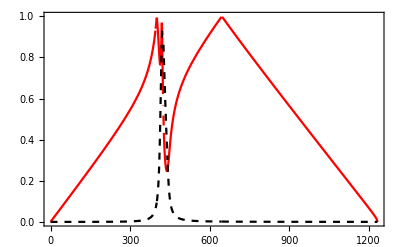

```mathematica
TrFunc[k_]:= Tr[M[k]]/2 ;
(*TrFunc[k_]:= Tr[M[k]]- Sqrt[Tr[M[k]]^2-4*Det[Tr[M[k]]]];*)
(*TraceM1[k_]:= (M11[k]+ M22[k])/2- Sqrt[((M11[k]+ M22[k])/2)^2+M12[k]+ M21[k]];*)

q[k_] :=ArcCos[ TrFunc[k]]/a;
q[k]//FullSimplify;
FullSimplify[%];
(*ToMatlab[%];*)
Plot[{Re[q[2*Pi*freq/c0]*a/Pi],Abs[Im[q[2*Pi*freq/c0]*a/Pi]]},{freq,0.1,f0},PlotRange->{{0,fc},{0,1}},PlotStyle->{Red,{Black,Dashed},Thick},Frame->True]
```

### Energy conserving = S-matrix is unitary

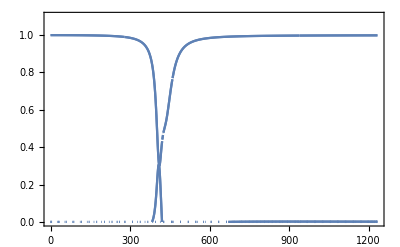

```mathematica
ReImPlot[SS[2*Pi*freq/c0].Transpose[Conjugate[SS[2*Pi*freq/c0]]],{freq,0.1,f0},PlotRange->{{0,f0},{0,1.1}},Frame->True]
```

### SU (1, 1) group?

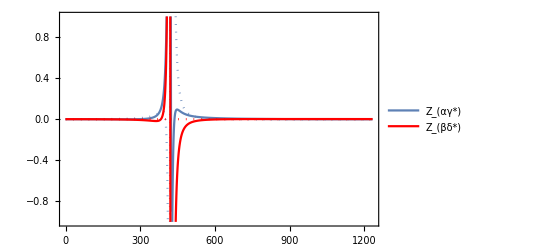

```mathematica
(*ReImPlot[M11[2*Pi*freq/c0]*M22[2*Pi*freq/c0] - M12[2*Pi*freq/c0]*M21[2*Pi*freq/c0] ,{freq,0.1,1200},PlotRange->{{0,1200},{0,1.1}},Frame->True]*)


alphaGamma[freq_]:= M11[2*Pi*freq/c0]-Conjugate[M22[2*Pi*freq/c0]];
meanAlphaGamma := Mean[alphaGamma[Range[0.1,f0,0.1]]];
stdAlphaGamma:= StandardDeviation[alphaGamma[Range[0.1,f0,1]]];

betaDelta[freq_]:= M12[2*Pi*freq/c0]-Conjugate[M21[2*Pi*freq/c0]];
meanBetaDelta := Mean[betaDelta[Range[0.1,f0,1]]];
stdBetaDelta:= StandardDeviation[betaDelta[Range[0.1,f0,1]]];


p1 = ReImPlot[(alphaGamma[freq]- 0*meanAlphaGamma)/stdAlphaGamma ,{freq,0.1,f0},PlotRange->{{0,f0},{-1,1}},Frame->True,PlotLegends->LineLegend[{"Z_(αγ*)"}]];
p2 = ReImPlot[(betaDelta[freq]- 0*meanBetaDelta)/stdBetaDelta ,{freq,0.1,f0},PlotRange->{{0,f0},{-1,1}},Frame->True,PlotLegends->LineLegend[{"Z_(βδ*)"}],PlotStyle->Red];
Show[p1,p2, PlotRange->All]

(*Mpow2[freq_]:=M[2*Pi*freq/c0]*M[2*Pi*freq/c0]
ReImPlot[{
Mpow2[freq][[1,2]]
(*M[2*Pi*freq/c0]*M[2*Pi*freq/c0][[1,2]],
M[2*Pi*freq/c0]*M[2*Pi*freq/c0][[2,1]],
M[2*Pi*freq/c0]*M[2*Pi*freq/c0][[2,2]]*)
},{freq,0.1,1200},PlotRange->{{0,1200},{-2,2}},Frame->True]*)
```

### Topology

```mathematica
AlphaR[k_]:= Re[M11[k]]
AlphaI[k_]:=Im[M11[k]]
BetaR[k_]:=Re[M21[k]]
BetaI[k_]:=Im[M21[k]]

coneplot = Plot3D[{Sqrt[x^2+y^2],-Sqrt[x^2+y^2]},{x,-2,2},{y,-2,2},
RegionFunction->Function[{x,y,z},x^2+y^2≤4],BoxRatios->Automatic,
ColorFunction->"RustTones",
PlotStyle->Opacity[0.5],
Mesh-> False,
Boxed->False,
Axes->False,
AxesOrigin->{0,0,0},
AxesStyle->Opacity[1],
TicksStyle->None,
AxesLabel->{Style[hi,16],Style[y,16],Style[z,16]},
ViewPoint->{Pi,Pi/2,2},Background->None]
(*Export["cone.png",coneplot,Background->None,ImageResolution-> 300]*)

Directory[]
```

-Graphics3D-

\\files7.epfl.ch\data\padlewsk\My Documents\PhD\acoustic-projects-master\active-dimer\simulation\mathematica\AA3